```mathematica
SetDirectory["/Users/marco/marco.live/DIDATTICA/CORSI/2023-2024/IN450/esoneri/ESO1"];
Get["/Users/marco/marco.live/DIDATTICA/CORSI/2023-2024/IN450/code/cryptolib.ma"]
testo=StringDrop[Import["testo.txt"],146];

CoincidenceIndex[testo]
plaintext=TextCode[testo];
Plus@@(Map[First,DistributionA[plaintext]]^2)
```

0.0729282

0.072929

```mathematica
ita=Import["http://www.corriere.it"];
divina="nelmezzodelcammindinostravitamiritrovaiperunaselvaoscuracheladirittaviaerasmarritaahiquantoadirqualeraecosaduraestaselvaselvaggiaeaspraefortechenelpensierrinovalapauratanteamarachepocoepiumortemapertrattardelbenchivitrovaidirodelaltrecosechivhoscorteiononsobenridircomivintraitanterapiendisonnoaquelpuntochelaveraceviaabbandonaimapoichifuialpieduncollegiuntoladoveterminavaquellavallechemaveadipaurailcorcompuntoguardaiinaltoevidilesuespallevestitegiaderaggidelpianetachemenadrittoaltruiperognecalleallorfulapauraunpocoquetachenellagodelcormeraduratalanottechipassaicontantapietaecomequeicheconlenaaffannatauscitofuordelpelagoalarivasivolgealacquaperigliosaeguatacosilanimomiochancorfuggivasivolsearetroarimirarlopassochenonlasciogiamaipersonavivapoicheiposatounpocoilcorpolassoripresiviaperlapiaggiadisertasichelpiefermosempreeralpiubassoedeccoquasialcominciardelertaunalonzaleggieraeprestamoltochedipelmacolatoeracovertaenonmisipartiadinanzialvoltoanzimpedivatantoilmiocamminochifuiperritornarpiuvoltevoltotemperadalprincipiodelmattinoelsolmontavansuconquellestellecheranconluiquandolamordivinomossediprimaquellecosebellesichabenesperarmeracagionediquellafieraalagaettapelleloradeltempoeladolcestagionemanonsichepauranonmidesselavistachemapparvedunleonequestipareachecontramevenisseconlatestaltaeconrabbiosafamesichepareachelaerenetremesseedunalupachedituttebramesembiavacarcanelasuamagrezzaemoltegentifegiavivergramequestamiporsetantodigravezzaconlapaurachusciadisuavistachioperdeilasperanzadelaltezzaequalequeichevolontieriacquistaegiugneltempocheperderlofacechentuttisuoipensierpiangeesattristatalmifecelabestiasanzapacechevenendomincontroapocoapocomiripignevaladovelsoltacementrechirovinavainbassolocodinanzialiocchimisifuoffertochiperlungosilenziopareafiocoquandovidicostuinelgrandisertomisereredimegridaialuiqualchetusiiodombraodomocertorispuoseminonomoomogiafuieliparentimieifuronlombardimantoaniperpatriaambeduinacquisubiulioancorchefossetardievissiaromasottolbuonoaugustoneltempodelideifalsiebugiardipoetafuiecantaidiquelgiustofigliuoldanchisechevenneditroiapoichelsuperboilionfucombustomatupercheritorniatantanoiaperchenonsaliildilettosomontecheprincipioecagiondituttagioiaorsetuquelvirgilioequellafontechespandidiparlarsilargofiumerispuosioluiconvergognosafronteodelialtripoetionoreelumevagliamillungostudioelgrandeamorechemhafattocercarlotuovolumetuselomiomaestroelmioautoretusesolocoluidacuiotolsilobellostilochemhafattoonorevedilabestiapercuiomivolsiaiutamidaleifamososaggiochellamifatremarleveneeipolsiateconvientenerealtroviaggiorispuosepoichelagrimarmividesevuocampardestolocoselvaggiochequestabestiaperlaqualtugridenonlasciaaltruipassarperlasuaviamatantolompediscecheluccideehanaturasimalvagiaeriachemainonempielabramosavogliaedopolpastohapiufamechepriamoltisonlianimaliacuisammogliaepiusarannoancorainfinchelveltroverrachelafaramorircondogliaquestinonciberaterranepeltromasapienzaamoreevirtuteesuanazionsaratrafeltroefeltrodiquellaumileitaliafiasalutepercuimorilaverginecammillaeurialoeturnoenisodiferutequestilacacceraperognevillafinchelavrarimessanelonfernolaondenvidiaprimadipartillaondioperlotuomepensoediscernochetumiseguieiosarotuaguidaetrarrottidiquiperlocoetternooveudirailedisperatestridavedrailiantichispiritidolentichalasecondamorteciascungridaevederaicolorchesoncontentinelfocoperchesperandivenirequandochesiaalebeategentialequaipoisetuvorraisalireanimafiaaciopiudimedegnaconleitilasceronelmiopartirechequelloimperadorchelasuregnaperchifuribellantealasualeggenonvuolchensuacittapermesivegnaintuttepartiimperaequivireggequivielasuacittaelaltoseggioohfelicecoluicuivieleggeeioaluipoetaiotiricheggioperquellodiochetunonconoscestiaciochiofuggaquestomaleepeggiochetumimeniladovordicestisichioveggialaportadisanpietroecolorcuitufaicotantomestiallorsimosseeiolitennidietro";

(* uso la distribuzione del testo per autocorrelare la parte estratta nel cifrato*)

refita=TextCode@divina;
mita=CoincidenceIndex[refita]
DistributionA[refita]


refita=plaintext;
mita=CoincidenceIndex[refita]
DistributionA[refita]
```

0.072238

{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00447604,Z},{0.0073723,B},{0.00947867,Q},{0.0123749,F},{0.0202738,H},{0.0221169,V},{0.0226435,G},{0.028436,D},{0.0326488,M},{0.0326488,P},{0.0416008,U},{0.0468668,C},{0.0468668,S},{0.0542391,N},{0.0576619,T},{0.0645076,L},{0.0647709,R},{0.087941,O},{0.106372,I},{0.11743,A},{0.119273,E}}

0.0729282

{{0.,J},{0.,K},{0.,W},{0.,Y},{8.77276×10^-7,X},{0.00472852,Z},{0.00639885,Q},{0.00925088,B},{0.01346,F},{0.016606,H},{0.0195124,V},{0.0230364,G},{0.0249945,M},{0.0274465,P},{0.0329198,U},{0.0372193,D},{0.0479458,C},{0.0519172,S},{0.0553456,T},{0.0626726,L},{0.0694241,N},{0.0715243,R},{0.0960591,O},{0.0978865,I},{0.114413,A},{0.117237,E}}

```mathematica
key=TextCode["spada"]
Print["Statistical Characteristics of plaintext blocks :"];
Map[DistributionA,blocks=Transpose@Partition[plaintext,m]]
ciphertext=Flatten@Transpose@Mod[blocks+key,26];FromCode@ciphertext
```

{18,15,0,3,0}

Statistical Characteristics of plaintext blocks :

{{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00453991,Z},{0.0064436,Q},{0.00954039,B},{0.0133127,F},{0.0168086,H},{0.0195501,V},{0.0224671,G},{0.0248006,M},{0.0281606,P},{0.0334111,U},{0.0379203,D},{0.047759,C},{0.0511935,S},{0.0556282,T},{0.0626727,L},{0.0697173,N},{0.0706823,R},{0.0958119,O},{0.0988867,I},{0.114472,A},{0.116222,E}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00469344,Z},{0.00636465,Q},{0.00919387,B},{0.0135759,F},{0.0164797,H},{0.0195107,V},{0.0234452,G},{0.025191,M},{0.0273798,P},{0.0330909,U},{0.0371308,D},{0.0479213,C},{0.0521059,S},{0.0549965,T},{0.0623788,L},{0.0696032,N},{0.0708753,R},{0.0956934,O},{0.0987376,I},{0.113546,A},{0.118086,E}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00450482,Z},{0.00632079,Q},{0.00915439,B},{0.0136636,F},{0.0166332,H},{0.0196686,V},{0.0230987,G},{0.0250331,M},{0.0275027,P},{0.0331479,U},{0.0370738,D},{0.0480134,C},{0.0523691,S},{0.0555799,T},{0.0627648,L},{0.0690286,N},{0.0718403,R},{0.0966541,O},{0.0972375,I},{0.11366,A},{0.117051,E}},{{0.,J},{0.,K},{0.,W},{0.,Y},{4.38639×10^-6,X},{0.00504435,Z},{0.00645676,Q},{0.00905351,B},{0.0134267,F},{0.0164665,H},{0.019151,V},{0.0233444,G},{0.024827,M},{0.0266912,P},{0.0323759,U},{0.0373369,D},{0.0478994,C},{0.0513822,S},{0.0554659,T},{0.0621156,L},{0.0693356,N},{0.0720684,R},{0.0965181,O},{0.098141,I},{0.115327,A},{0.117568,E}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00486012,Z},{0.00640851,Q},{0.0093123,B},{0.0133215,F},{0.016642,H},{0.0196817,V},{0.0228268,G},{0.0251208,M},{0.0274983,P},{0.0325733,U},{0.0366351,D},{0.0481362,C},{0.0525314,S},{0.0550579,T},{0.0634316,L},{0.0694365,N},{0.0721561,R},{0.0956189,O},{0.0964304,I},{0.115059,A},{0.117261,E}}}

5

Statistical Characteristics of plaintext blocks :

{{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00453991,Z},{0.0064436,Q},{0.00954039,B},{0.0133127,F},{0.0168086,H},{0.0195501,V},{0.0224671,G},{0.0248006,M},{0.0281606,P},{0.0334111,U},{0.0379203,D},{0.047759,C},{0.0511935,S},{0.0556282,T},{0.0626727,L},{0.0697173,N},{0.0706823,R},{0.0958119,O},{0.0988867,I},{0.114472,A},{0.116222,E}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00469344,Z},{0.00636465,Q},{0.00919387,B},{0.0135759,F},{0.0164797,H},{0.0195107,V},{0.0234452,G},{0.025191,M},{0.0273798,P},{0.0330909,U},{0.0371308,D},{0.0479213,C},{0.0521059,S},{0.0549965,T},{0.0623788,L},{0.0696032,N},{0.0708753,R},{0.0956934,O},{0.0987376,I},{0.113546,A},{0.118086,E}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00450482,Z},{0.00632079,Q},{0.00915439,B},{0.0136636,F},{0.0166332,H},{0.0196686,V},{0.0230987,G},{0.0250331,M},{0.0275027,P},{0.0331479,U},{0.0370738,D},{0.0480134,C},{0.0523691,S},{0.0555799,T},{0.0627648,L},{0.0690286,N},{0.0718403,R},{0.0966541,O},{0.0972375,I},{0.11366,A},{0.117051,E}},{{0.,J},{0.,K},{0.,W},{0.,Y},{4.38639×10^-6,X},{0.00504435,Z},{0.00645676,Q},{0.00905351,B},{0.0134267,F},{0.0164665,H},{0.019151,V},{0.0233444,G},{0.024827,M},{0.0266912,P},{0.0323759,U},{0.0373369,D},{0.0478994,C},{0.0513822,S},{0.0554659,T},{0.0621156,L},{0.0693356,N},{0.0720684,R},{0.0965181,O},{0.098141,I},{0.115327,A},{0.117568,E}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00486012,Z},{0.00640851,Q},{0.0093123,B},{0.0133215,F},{0.016642,H},{0.0196817,V},{0.0228268,G},{0.0251208,M},{0.0274983,P},{0.0325733,U},{0.0366351,D},{0.0481362,C},{0.0525314,S},{0.0550579,T},{0.0634316,L},{0.0694365,N},{0.0721561,R},{0.0956189,O},{0.0964304,I},{0.115059,A},{0.117261,E}}}

0.0729282

0.0729282

Statistical Characteristics of ciphertext blocks :

0.0517875

{0.0728084,0.0729256,0.072799,0.0732198,0.0728907}

{{{0.,B},{0.,C},{0.,O},{0.,P},{0.,Q},{0.00453991,R},{0.0064436,I},{0.00954039,T},{0.0133127,X},{0.0168086,Z},{0.0195501,N},{0.0224671,Y},{0.0248006,E},{0.0281606,H},{0.0334111,M},{0.0379203,V},{0.047759,U},{0.0511935,K},{0.0556282,L},{0.0626727,D},{0.0697173,F},{0.0706823,J},{0.0958119,G},{0.0988867,A},{0.114472,S},{0.116222,W}},{{0.,L},{0.,M},{0.,N},{0.,Y},{0.,Z},{0.00469344,O},{0.00636465,F},{0.00919387,Q},{0.0135759,U},{0.0164797,W},{0.0195107,K},{0.0234452,V},{0.025191,B},{0.0273798,E},{0.0330909,J},{0.0371308,S},{0.0479213,R},{0.0521059,H},{0.0549965,I},{0.0623788,A},{0.0696032,C},{0.0708753,G},{0.0956934,D},{0.0987376,X},{0.113546,P},{0.118086,T}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00450482,Z},{0.00632079,Q},{0.00915439,B},{0.0136636,F},{0.0166332,H},{0.0196686,V},{0.0230987,G},{0.0250331,M},{0.0275027,P},{0.0331479,U},{0.0370738,D},{0.0480134,C},{0.0523691,S},{0.0555799,T},{0.0627648,L},{0.0690286,N},{0.0718403,R},{0.0966541,O},{0.0972375,I},{0.11366,A},{0.117051,E}},{{0.,B},{0.,M},{0.,N},{0.,Z},{4.38639×10^-6,A},{0.00504435,C},{0.00645676,T},{0.00905351,E},{0.0134267,I},{0.0164665,K},{0.019151,Y},{0.0233444,J},{0.024827,P},{0.0266912,S},{0.0323759,X},{0.0373369,G},{0.0478994,F},{0.0513822,V},{0.0554659,W},{0.0621156,O},{0.0693356,Q},{0.0720684,U},{0.0965181,R},{0.098141,L},{0.115327,D},{0.117568,H}},{{0.,J},{0.,K},{0.,W},{0.,X},{0.,Y},{0.00486012,Z},{0.00640851,Q},{0.0093123,B},{0.0133215,F},{0.016642,H},{0.0196817,V},{0.0228268,G},{0.0251208,M},{0.0274983,P},{0.0325733,U},{0.0366351,D},{0.0481362,C},{0.0525314,S},{0.0550579,T},{0.0634316,L},{0.0694365,N},{0.0721561,R},{0.0956189,O},{0.0964304,I},{0.115059,A},{0.117261,E}}}

{0.0356642,0.0418672,0.072865,0.0356318,0.0729095}

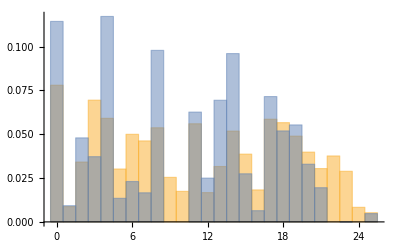

```mathematica
m=Length@key

Print["Statistical Characteristics of plaintext blocks :"];
Map[DistributionA,blocks=Transpose@Partition[plaintext,m]]

CoincidenceIndex[refita]
CoincidenceIndex[plaintext]

Print["Statistical Characteristics of ciphertext blocks :"];
MutualInformation[ciphertext,refita]
Map[CoincidenceIndex,blocks=Transpose@Partition[ciphertext,m]]

Map[DistributionA,blocks]
Map[MutualInformation[#,refita]&,blocks]
Histogram[{ciphertext,refita},26,"Probability"]
```

```mathematica
CoincidenceIndex[testo_,trunc_,n_]:=
If[
StringQ[testo],
(*THEN*)
CoincidenceIndex[TextCode[testo],trunc,n],
(*ELSE*)
Module[{ntesto,tfreqs},
(
ntesto=Take[testo,n];
tfreqs=Take[Sort[Map[Count[ntesto,#]&,Range[0,25]]],-trunc];
N[Plus@@(tfreqs(tfreqs-1)/(n (n-1)))]
)]
]
```

```mathematica
random=Table[RandomInteger[25],{2500}];
```

```mathematica
G=ListLinePlot[Transpose@Table[Map[CoincidenceIndex[#,10,len]&,Prepend[blocks,random]],{len,10,200}],PlotRange->All];

wblocks=Transpose@Partition[ciphertext,m-1];
Gwrong=ListLinePlot[Transpose@Table[Map[CoincidenceIndex[#,10,len]&,Prepend[wblocks,random]],{len,10,200}],PlotStyle->{Thick,Opacity[0.1]},PlotRange->All];
```

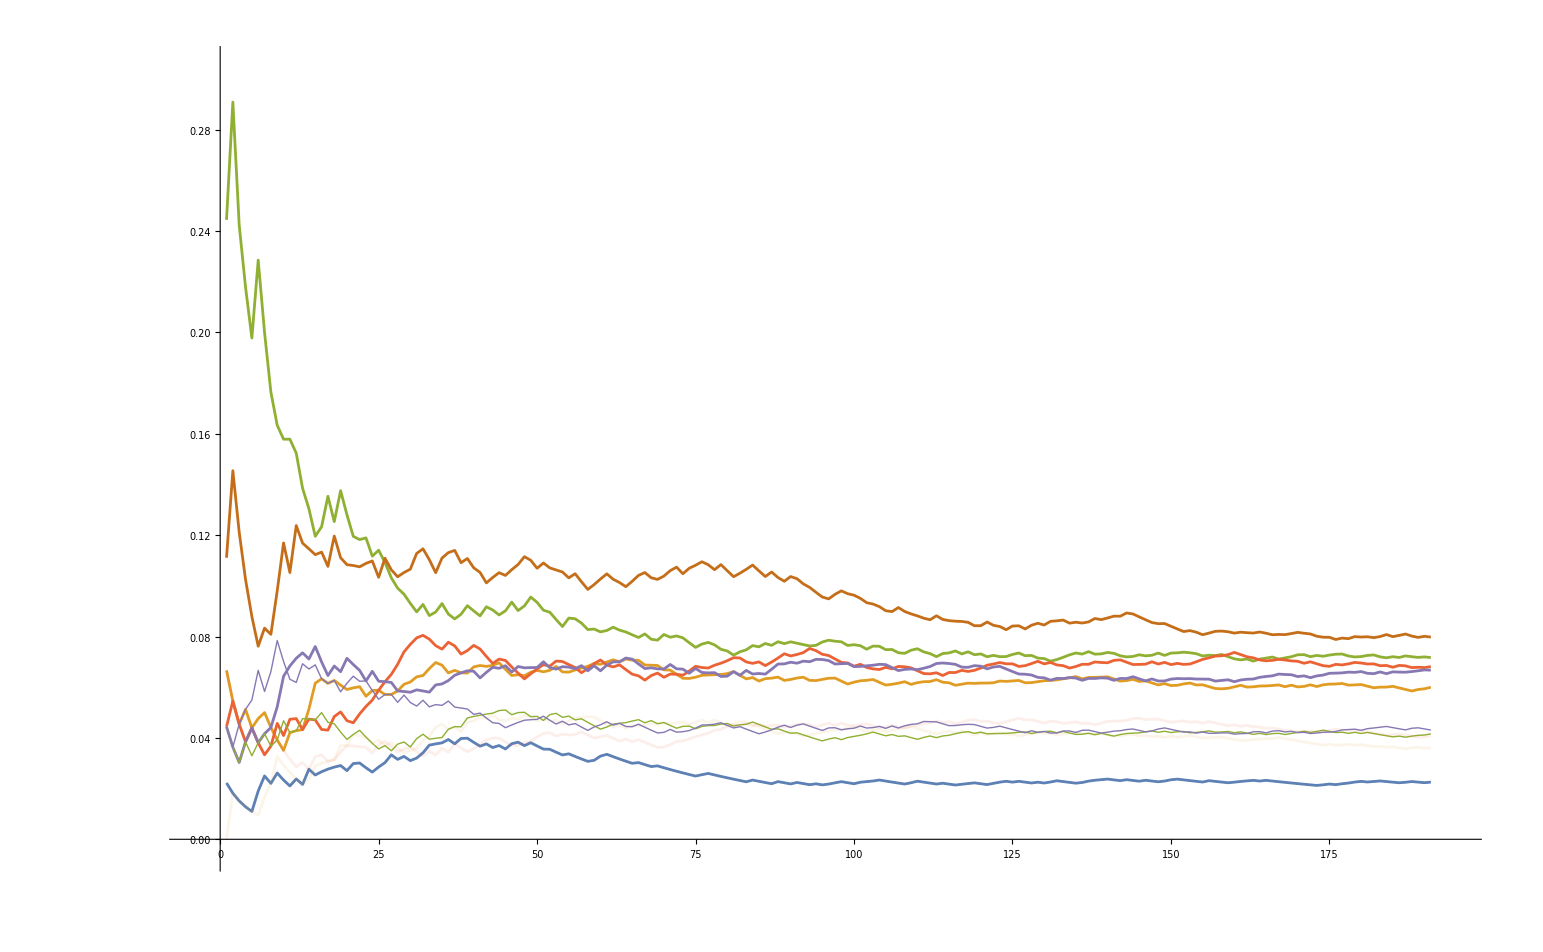

```mathematica
Show[G,Gwrong]
```